```mathematica
Quit[]
```

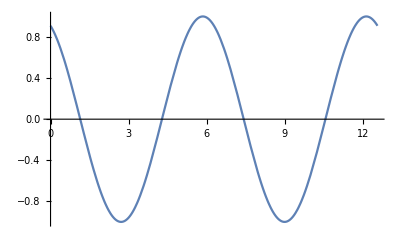

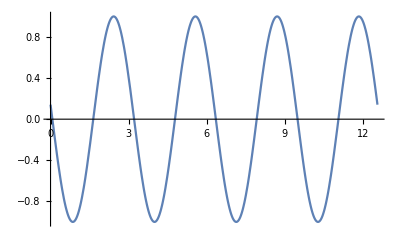

```mathematica
f[a_,b_]:=Plot[Sin[a*x+b],{x,0,4*Pi}]
f[1,2]
f[2,3]
```

```mathematica
Manipulate[f[par1,par2],{{par1,1,"a"},0, 2,0.01,Appearance->"Labeled"},{{par2,1,"b"},0.2, 3,0.01,Appearance->"Labeled"}]
```

```mathematica
Manipulate[f[par1,par2],{{par1,0},0, 2,0.01,Appearance->"Labeled"},{{par2,0.2},0.2, 3,0.01,Appearance->"Labeled"}]
```